```mathematica
<<peeters`

peeters`setGitDir["../project/figures/phy487-qmsolids"]

fs=Style[#,FontSize->14]&;
```

C:\Users\Peeter\cygwin_home\physicsplay\notes\blogit

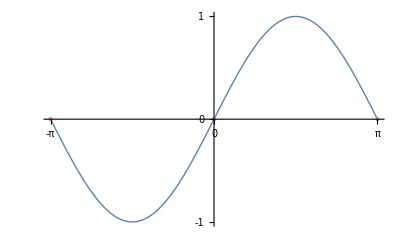
{-Graphics-,{discreteFourierRangeFig1.eps,discreteFourierRangeFig1pn.png}}

```mathematica
Module[{ p, g, b }, 
p = Plot[Sin[x],{x, -Pi, Pi}, Ticks -> {{-Pi, 0, Pi}, {-1, 0, 1}},
PlotStyle->Thick
] ;
g = Graphics[{PointSize[Large],Pink, Point[{#, 0} &/@ { -Pi, 0, Pi} ] 
}] ;

b = Show[p, g] ;

{b, peeters`exportForLatex["discreteFourierRangeFig1", b] }
]
```